```mathematica
ABMInputs800=Import["/Users/thorsilver/Downloads/ABM outputs1/LPtau800runs_GEMSA_inputs.csv"];

ABMOutputs800=Import["/Users/thorsilver/Downloads/ABM outputs1/LPtau800runs GEMSA outputs only.csv"];
```

```mathematica
ABMOutputs800=Function[x,x/1000]/@ABMOutputs800;
ABMAssoc800 = AssociationThread[ABMInputs800 -> Flatten[ABMOutputs800]];
ABMnewData800=Dataset[ABMAssoc800];
ABMNormal800=Normal[ABMAssoc800];
ABMNormalRandom=RandomSample[ABMNormal800];
ABMtrain800=TakeDrop[ABMNormal800,640];
ABMtest800=ABMtrain800[[2]];
ABMtraining800=ABMtrain800[[1]];
trainDevSplit800=TakeDrop[ABMtraining800,512];
finalTrain800=trainDevSplit800[[1]];
finalDev800=trainDevSplit800[[2]];
finaltest800=ABMtest800;
```

```mathematica
Length[finalDev800]
Length[finalTrain800]
Length[finaltest800]
```

128

512

160

## Predictor Comparisons

```mathematica
pRFv800=Predict[finalTrain800,Method->"RandomForest"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

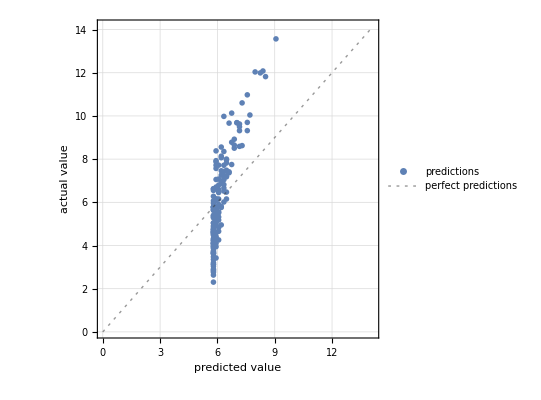

```mathematica
pmRFv800=PredictorMeasurements[pRFv800,finaltest800]
pmRFv800["ComparisonPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

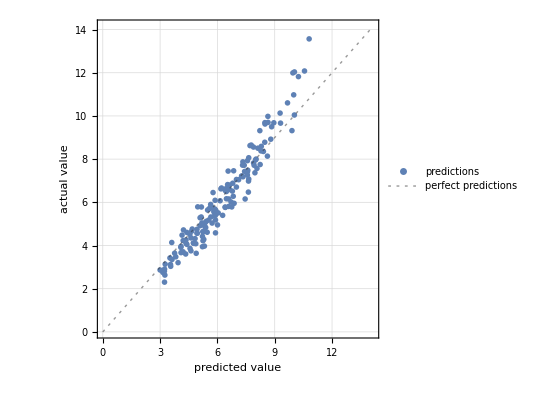

```mathematica
pXGTv800=Predict[finalTrain800,Method->"GradientBoostedTrees"]
pmXGTv800=PredictorMeasurements[pXGTv800,finaltest800]
pmXGTv800["ComparisonPlot"]
```

```mathematica
pNNv800= Predict[finalTrain800,Method->{"NeuralNetwork", "NetworkDepth"->3,"NetworkType"->"FullyConnected", "L2Regularization"->0.05, MaxTrainingRounds->16000}]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

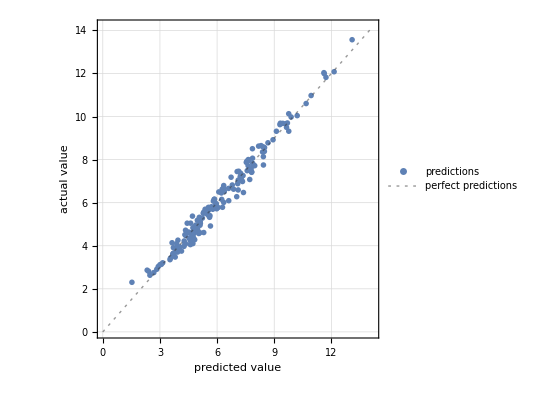

```mathematica
pmNNv800=PredictorMeasurements[pNNv800,finaltest800]
pmNNv800["ComparisonPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

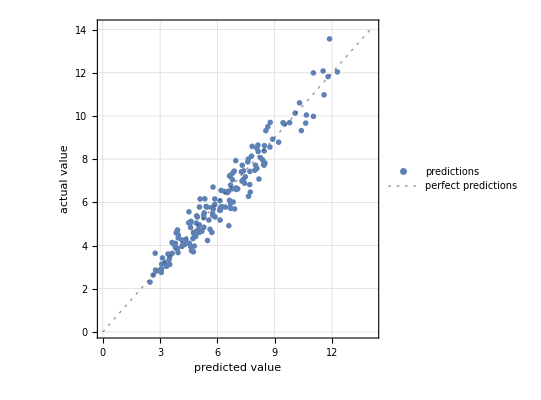

```mathematica
pGPEv800=Predict[finalTrain800,Method->"GaussianProcess"]
pmGPEv800=PredictorMeasurements[pGPEv800,finaltest800]
pmGPEv800["ComparisonPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

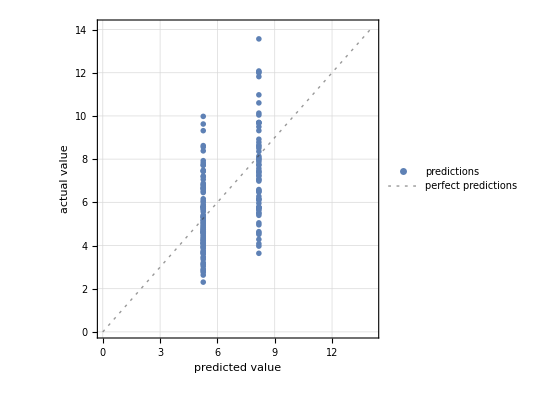

```mathematica
pDTv800=Predict[finalTrain800,Method->"DecisionTree"]
pmDTv800=PredictorMeasurements[pDTv800,finaltest800]
pmDTv800["ComparisonPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

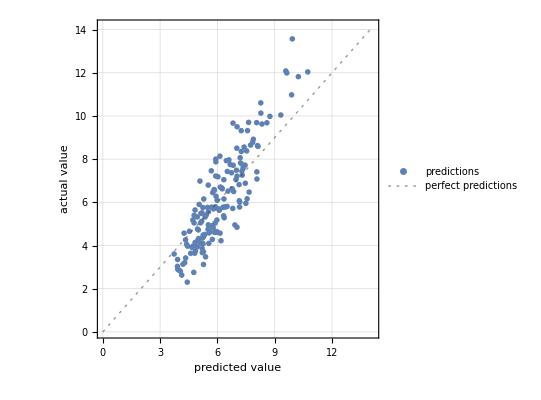

```mathematica
pNearestv800=Predict[finalTrain800,Method->"NearestNeighbors"]
pmNearestv800=PredictorMeasurements[pNearestv800,finaltest800]
pmNearestv800["ComparisonPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

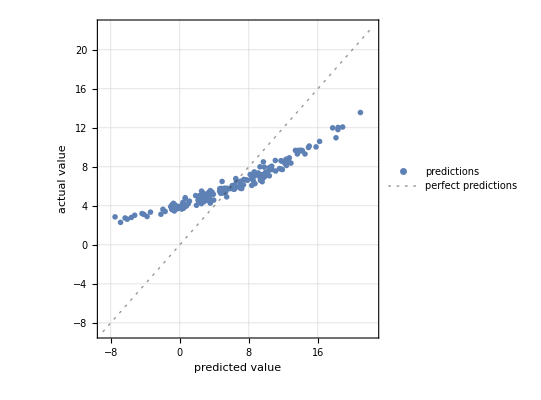

```mathematica
pLRv800=Predict[finalTrain800,Method->"LinearRegression"]
pmLRv800=PredictorMeasurements[pLRv800,finaltest800]
pmLRv800["ComparisonPlot"]
```

### Residual Plots

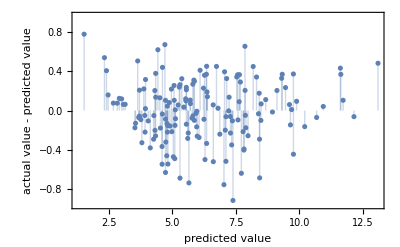

```mathematica
pmNNv800["ResidualPlot"]
```

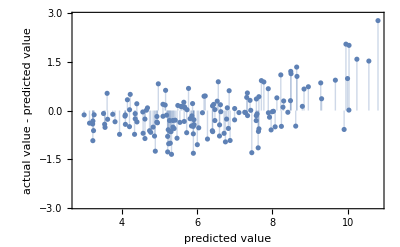

```mathematica
pmXGTv800["ResidualPlot"]
```

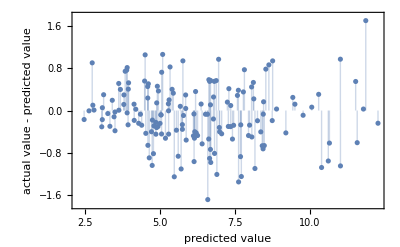

```mathematica
pmGPEv800["ResidualPlot"]
```

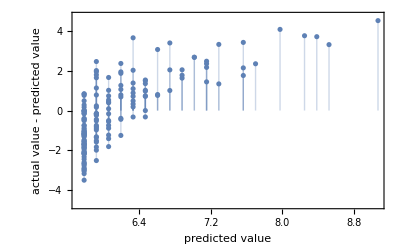

```mathematica
pmRFv800["ResidualPlot"]
```

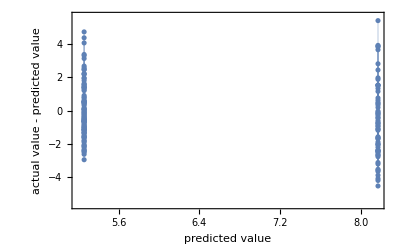

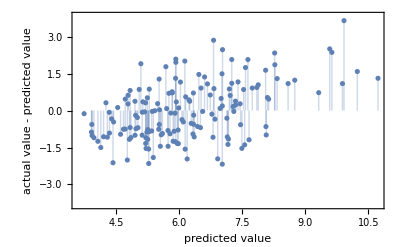

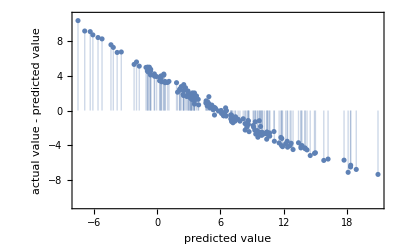

```mathematica
pmDTv800["ResidualPlot"]
pmNearestv800["ResidualPlot"]
pmLRv800["ResidualPlot"]
```

### MeanSquare

```mathematica
pmNNv800["MeanSquare"]
pmDTv800["MeanSquare"]
pmLRv800["MeanSquare"]
pmRFv800["MeanSquare"]
pmXGTv800["MeanSquare"]
pmGPEv800["MeanSquare"]
pmLRv800["MeanSquare"]
pmNearestv800["MeanSquare"]
```

0.0965913

3.85457

13.4386

2.9742

0.45184

0.329983

13.4386

1.35636

### Predictor Summaries

```mathematica
Information[pNNv800]
Information[pXGTv800]
Information[pGPEv800]
Information[pRFv800]
```

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 1.34 ± 0.63
Method | NeuralNetwork
Single evaluation time | 2.18 ms/example
Batch evaluation speed | 49.2 examples/ms
Loss | 1.1 ± 0.16
Model memory | 251. kB
Training examples used | 512 examples
Training time | 3 48
 |

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 1.52 ± 0.52
Method | GradientBoostedTrees
Single evaluation time | 3.79 ms/example
Batch evaluation speed | 50.5 examples/ms
Loss | 1.56 ± 0.15
Model memory | 391. kB
Training examples used | 512 examples
Training time | 1.5 s
 |

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 1.39 ± 0.3
Method | GaussianProcess
Single evaluation time | 3.95 ms/example
Batch evaluation speed | 22.8 examples/ms
Loss | 1.57 ± 0.19
Model memory | 1.59 MB
Training examples used | 512 examples
Training time | 4.12 s
 |

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 3.01 ± 0.18
Method | RandomForest
Single evaluation time | 4.61 ms/example
Batch evaluation speed | 34.3 examples/ms
Loss | 2.53 ± 0.055
Model memory | 257. kB
Training examples used | 512 examples
Training time | 1.58 s
 |

```mathematica
Information[pDTv800]
Information[pNearestv800]
Information[pLRv800]
```

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 3.64 ± 0.24
Method | DecisionTree
Single evaluation time | 1.28 ms/example
Batch evaluation speed | 418. examples/ms
Loss | 2.68 ± 0.042
Model memory | 149. kB
Training examples used | 512 examples
Training time | 532. ms
 |

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 3.15 ± 0.39
Method | NearestNeighbors
Single evaluation time | 1.6 ms/example
Batch evaluation speed | 84. examples/ms
Loss | 2.75 ± 0.19
Model memory | 188. kB
Training examples used | 512 examples
Training time | 370. ms
 |

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.54 ± 0.15
Method | LinearRegression
Single evaluation time | 1.54 ms/example
Batch evaluation speed | 288. examples/ms
Loss | 2.34 ± 0.042
Model memory | 263. kB
Training examples used | 512 examples
Training time | 1.42 s
 |